## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_GAPD_typeI";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0.7,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
0.7 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,Overscript[(GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c, GAPD2],((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,Overscript[(GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c, GAPD4],((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Build enzyme model

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};


inhibitionListSubset=inhibitionList;
customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}};

simulateDataFlag="normal";
nSamples=Null;
paramScanList=Null;

numFits=5;
 flagFitType="log_ssd";
```

```mathematica
{fittingData, filteredDataList, bestFitDetails,dataFilePathList,
{enzymeModelLocal, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub,
	allCatalyticReactions,nonCatalyticReactions, absoluteFlux, absoluteRateForward,
absoluteRateReverse, relativeRateForward, relativeRateReverse, 
	otherAbsoluteRatesForward, otherAbsoluteRatesReverse}}=
buildFullEnzymeModel[enzymeModel, rxn, pathMASSef, inputPath, outputPath, dataFileName, inhibitionList,inhibitionList, KeqList, kmList, 
					 s05List, kcatList,inhibitionList, activationList, otherParmsList,inhibitionListSubset,bufferInfo, ionCharge,
					 catalyticReactionsSetsList, otherMetsReverseZeroSub,  otherMetsForwardZeroSub,   customRatiosDataList, MWCFlag,
					simplifyFlag, simplifyMaxTime, nActiveSites, fitLabel, numFits, simulateDataFlag, nSamples, paramScanList,
					assumedSaturatingConc, flagFitType];
```

Added inhibition reactions:

{}

Generating flux equation...

{((GAPD^c&nad^c&g3p^c&pi^c)_^-((GAPD^c&nadh^c&(13dpg)^c)_^)/K_GAPD6) Volume_c k_GAPD6^⟶}

Volume_c (-(GAPD^c&nadh^c&(13dpg)^c)_^ k_GAPD6^⟵+(GAPD^c&nad^c&g3p^c&pi^c)_^ k_GAPD6^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Configuring enzyme fits...

Running enzyme fit...

5

Evaluating fitness results...

End

## Evaluate fit results

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | relRateFor_nad | 7.25426×10^-6 | 5.26242×10^-11 | 1.51849×10^-6 | 0.00167034 | 0.0909091 | 0.0909076
1 | relRateFor_nad | 5.90131×10^-6 | 3.48255×10^-11 | 1.85896×10^-6 | 0.00135882 | 0.136807 | 0.136805
1 | relRateFor_nad | 4.01613×10^-6 | 1.61293×10^-11 | 1.85652×10^-6 | 0.000924745 | 0.20076 | 0.200758
1 | relRateFor_nad | 1.54039×10^-6 | 2.3728×10^-12 | 1.00996×10^-6 | 0.000354687 | 0.284747 | 0.284746
1 | relRateFor_nad | 1.46977×10^-6 | 2.16021×10^-12 | 1.30925×10^-6 | 0.000338427 | 0.386863 | 0.386864
1 | relRateFor_nad | 4.80482×10^-6 | 2.30863×10^-11 | 5.53178×10^-6 | 0.00110636 | 0.5 | 0.500006
1 | relRateFor_nad | 8.13989×10^-6 | 6.62579×10^-11 | 0.000011492 | 0.0018743 | 0.613137 | 0.613148
1 | relRateFor_nad | 0.0000111501 | 1.24325×10^-10 | 0.0000183637 | 0.00256744 | 0.715253 | 0.715271
1 | relRateFor_nad | 0.0000136259 | 1.85666×10^-10 | 0.0000250765 | 0.00313754 | 0.79924 | 0.799265
1 | relRateFor_nad | 0.0000155112 | 2.40598×10^-10 | 0.0000308302 | 0.00357165 | 0.863193 | 0.863224
1 | relRateFor_nad | 0.0000168642 | 2.84402×10^-10 | 0.0000353019 | 0.00388321 | 0.909091 | 0.909126
0.7 | relRateFor_g3p | 0.000142202 | 2.02213×10^-8 | 0.0000297616 | 0.0327378 | 0.0909091 | 0.0908793
0.7 | relRateFor_g3p | 0.000115506 | 1.33416×10^-8 | 0.0000363806 | 0.0265926 | 0.136807 | 0.136771
0.7 | relRateFor_g3p | 0.0000783053 | 6.13172×10^-9 | 0.0000361947 | 0.0180288 | 0.20076 | 0.200724
0.7 | relRateFor_g3p | 0.0000294465 | 8.67096×10^-10 | 0.0000193061 | 0.00678007 | 0.284747 | 0.284728
0.7 | relRateFor_g3p | 0.0000299659 | 8.97955×10^-10 | 0.0000266941 | 0.00690014 | 0.386863 | 0.38689
0.7 | relRateFor_g3p | 0.0000957999 | 9.17762×10^-9 | 0.000110306 | 0.0220612 | 0.5 | 0.50011
0.7 | relRateFor_g3p | 0.000161644 | 2.61287×10^-8 | 0.000228251 | 0.0372268 | 0.613137 | 0.613365
0.7 | relRateFor_g3p | 0.000221082 | 4.88774×10^-8 | 0.0003642 | 0.0509191 | 0.715253 | 0.715617
0.7 | relRateFor_g3p | 0.000269975 | 7.28864×10^-8 | 0.000496994 | 0.0621833 | 0.79924 | 0.799737
0.7 | relRateFor_g3p | 0.000307208 | 9.4377×10^-8 | 0.000610816 | 0.0707624 | 0.863193 | 0.863804
0.7 | relRateFor_g3p | 0.000333932 | 1.11511×10^-7 | 0.000699275 | 0.0769203 | 0.909091 | 0.90979
1 | relRateFor_pi | 0.0000859946 | 7.39508×10^-9 | 0.0000179991 | 0.019799 | 0.0909091 | 0.0908911
1 | relRateFor_pi | 0.0000700312 | 4.90437×10^-9 | 0.0000220587 | 0.016124 | 0.136807 | 0.136785
1 | relRateFor_pi | 0.0000477872 | 2.28361×10^-9 | 0.0000220892 | 0.0110028 | 0.20076 | 0.200738
1 | relRateFor_pi | 0.0000185731 | 3.4496×10^-10 | 0.0000121773 | 0.00427652 | 0.284747 | 0.284735
1 | relRateFor_pi | 0.0000169495 | 2.87284×10^-10 | 0.0000150986 | 0.00390283 | 0.386863 | 0.386878
1 | relRateFor_pi | 0.0000563092 | 3.17073×10^-9 | 0.0000648326 | 0.0129665 | 0.5 | 0.500065
1 | relRateFor_pi | 0.0000956725 | 9.15323×10^-9 | 0.000135085 | 0.0220318 | 0.613137 | 0.613272
1 | relRateFor_pi | 0.000131204 | 1.72146×10^-8 | 0.000216117 | 0.0302155 | 0.715253 | 0.715469
1 | relRateFor_pi | 0.000160431 | 2.5738×10^-8 | 0.000295298 | 0.0369473 | 0.79924 | 0.799535
1 | relRateFor_pi | 0.000182686 | 3.33743×10^-8 | 0.000363179 | 0.0420739 | 0.863193 | 0.863556
1 | relRateFor_pi | 0.00019866 | 3.94657×10^-8 | 0.000415941 | 0.0457535 | 0.909091 | 0.909507
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.

### Simulated Data and Best Fit Data Plot

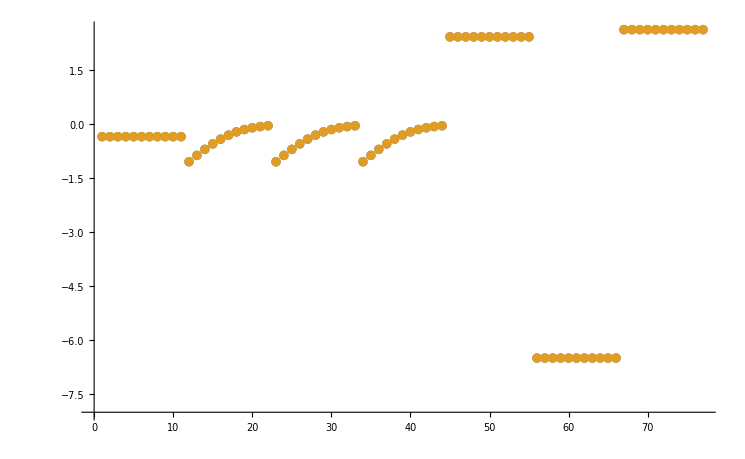

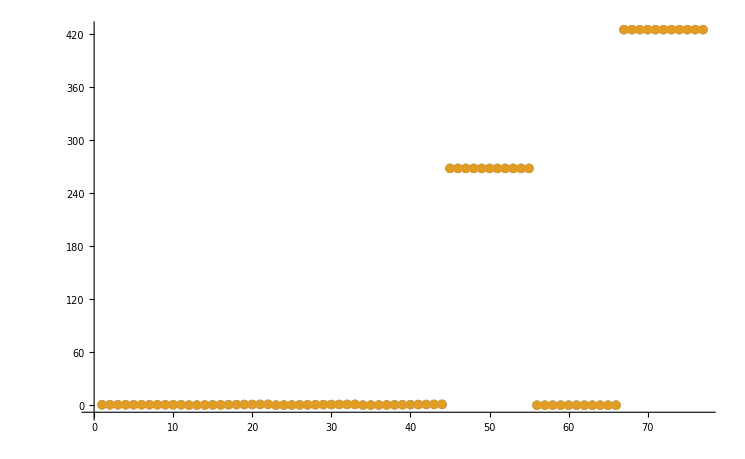

```mathematica
dataSetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

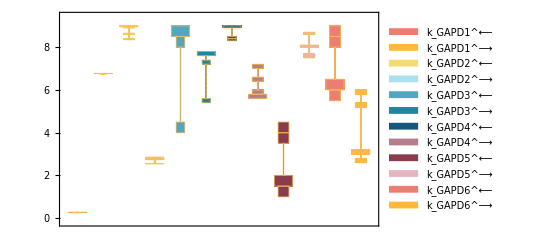

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

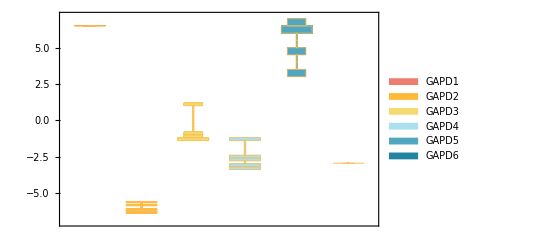

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

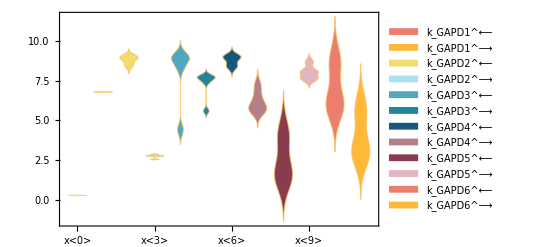

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

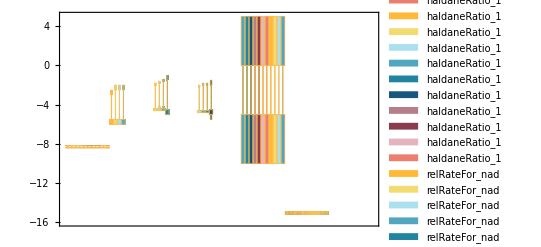

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePathList][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000045 | 0.000044999 | 0.00221259
0.00089 | 0.000889608 | 0.0440734
0.00053 | 0.000529863 | 0.0259159

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 7.91258×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 1.40397×10^-6

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

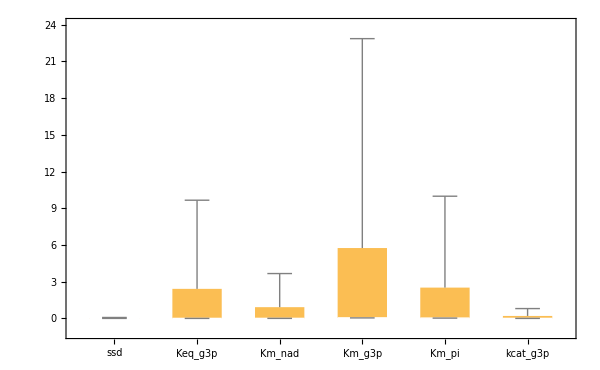

```mathematica
dataHeader = Import[dataFilePathList][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```